```mathematica
R=1;
u0[r_,θ_]:=((R^2-r^2)(Cos[θ])^2+r^2Log[r/R]+0.5*(r^2-R^2))/r^2;
v0[r_,θ_]:=((R^2-r^2)Sin[θ]Cos[θ])/r^2;

Manipulate[PolarPlot[{u[r,θ](*, v[r,θ]*)},{θ,-Pi,Pi}], {r, 1,10}]
```

General::ivar: -1.26263 is not a valid variable.

General::ivar: 3.29691 is not a valid variable.

General::ivar: -1.26262 is not a valid variable.

General::stop: Further output of General::ivar will be suppressed during this calculation.

General::ivar: -1.26263 is not a valid variable.

General::ivar: 3.29691 is not a valid variable.

General::ivar: -1.26262 is not a valid variable.

General::stop: Further output of General::ivar will be suppressed during this calculation.

General::ivar: -1.26263 is not a valid variable.

General::ivar: -1.26262 is not a valid variable.

General::stop: Further output of General::ivar will be suppressed during this calculation.

```mathematica
u[2,1]
```

0.849202

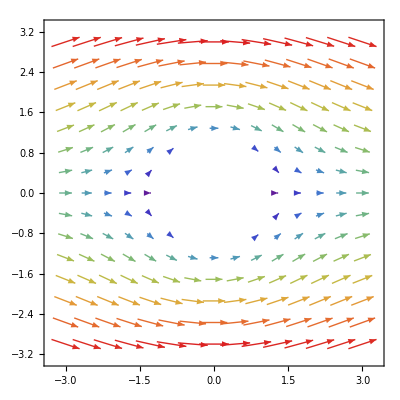

```mathematica
u[x_,y_]:=Module[{r=Sqrt[x^2+y^2], θ=ArcTan[x,y]},If[r≥ R,u0[r,θ],0]]
v[x_,y_]:=Module[{r=Sqrt[x^2+y^2], θ=ArcTan[x,y]},If[r≥R,v0[r,θ],0]]
VectorPlot[{u[x,y],v[x,y]},{x,-3,3},{y,-3,3},VectorColorFunction->"Rainbow"]
```

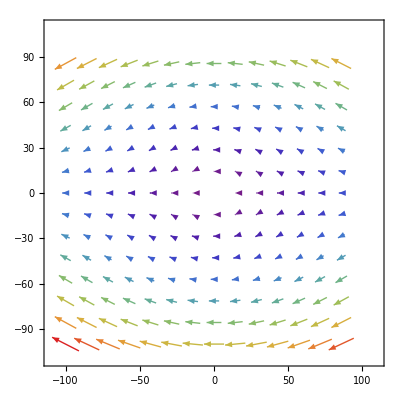

```mathematica
L=b/a;
L=1.01; λ=0; U=1; a=1;
boxs=100;
P=Log[L]-3/4;
Kk=2*λ*(P+0.5+0.25/L^4) + a*(P+1/L^2-0.25/L^4);
Aa=(U*a^2)/(2Kk)(λ/L^2 + a*(1-0.5/L^2));
Bb=-(U*a)/(2Kk)(1-1/L^2);
Cc=U/Kk(2*λ+a);
Dd=-U/(4a^2L^2Kk)(2*λ+a);
ψ[r_,θ_]:=(Aa/r + Bb*r + Cc*r*Log[r/a] + Dd*r^3)*Sin[θ]

ur[r_,θ_]:=D[ψ[r,θ1],θ1]/r/.θ1->θ;
uth[r_,θ_]:=-D[ψ[r1,θ],r1]/.r1->r;

u[x_,y_]:=Module[{r=Sqrt[x^2+y^2], θ=ArcTan[x,y]},If[r≥ R,ur[r,θ]*Cos[θ]-uth[r,θ]*Sin[θ],0]]
v[x_,y_]:=Module[{r=Sqrt[x^2+y^2], θ=ArcTan[x,y]},If[r≥R,ur[r,θ]*Sin[θ]+uth[r,θ]*Cos[θ],0]]
VectorPlot[{u[x,y],v[x,y]},{x,-boxs,boxs},{y,-boxs,boxs},VectorColorFunction->"Rainbow"]
```

```mathematica
ur[r,r]
```

General::ivar: 1 is not a valid variable.

(∂_1 ((196985./r-7612.76 r-189372. r^3+772714. r Log[r]) Sin[1]))/r

(765102.-196985./r^2-568117. r^2+772714. Log[r]) Sin[θ]